# Nematic fluids of discs mixed with shape-persistent living polymers

## Initialization

```mathematica
Clear["Global`*"]
```

Define some fixed parameters:

```mathematica
eb=1;
qq = (1+√(1+4*4*Exp[-eb]))/2;
zz = ((1+√(1+4*4*Exp[-eb]))/2)^2;
precision=50;
```

Definition of functions:

```mathematica
(* alignment amplitudes *)

ar[rr0_, rd0_, srav_, sd_]:=(5/4)*(rr0*srav-2*qq*rd0*sd);
ad[rr0_, rd0_, srav_, sd_]:=(5/4)*(zz*rd0*sd-2*qq*rr0*srav);

(* chi parameter for weakly flexible  rods *)

xi[lp_, rr0_, rd0_, srav_, sd_]:=1+Abs[ar[rr0, rd0, srav, sd]]+lp-√(1+2*lp+2*Abs[ar[rr0, rd0, srav, sd]]*lp+lp^2);
(* effective amplitude *)

arbar[lp_, rr0_, rd0_, srav_, sd_]:=ar[rr0, rd0, srav, sd]-Sign[ar[rr0, rd0, srav, sd]]*xi[lp, rr0, rd0, srav, sd];
(* polymer length distribution *)
rl[lp_, eb_, rr0_, rd0_, srav_, sd_, lambda_, ll_]:=ll*Exp[SetPrecision[eb+lambda*ll,precision]]*Exp[SetPrecision[arbar[lp, rr0, rd0, srav, sd]*ll,precision]]*DawsonF[SetPrecision[√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2),precision]]/(√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2));
(* nematic order parameters *)
srl[lp_, rr0_, rd0_, srav_, sd_, ll_]:=1/4 (-2-2/(arbar[lp, rr0, rd0, srav, sd]*ll)+(√6)/(√(arbar[lp, rr0, rd0, srav, sd]*ll) DawsonF[SetPrecision[√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2),precision]]));
sdf[rr0_, rd0_, srav_, sd_]:=1/4 (-2-2/ad[rr0, rd0, srav, sd]+(√6)/(√ad[ rr0, rd0, srav, sd] DawsonF[SetPrecision[√((3*ad[rr0, rd0, srav, sd])/2),precision]]));
```

## Polymer Distributions in the Nematic Phase

Equation system to obtain OverBar[S_r], S_d and λ:

```mathematica
solveConditions[lp_, eb_,rr0_,rd0_,llmax_, sravs_, sds_, lambdas_]:=FindRoot[{
Sum[rl[lp, eb, rr0, rd0, srav, sd, lambda, ll],{ll,1,llmax}]==rr0,
rr0^-1*Sum[srl[lp, rr0, rd0, srav, sd, ll]*rl[lp, eb, rr0, rd0, srav, sd, lambda, ll],{ll,1,llmax}]==srav,
sdf[rr0,rd0,srav,sd]==sd
},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}}];
```

### Plot

-3.36381

0.928426

-0.468574

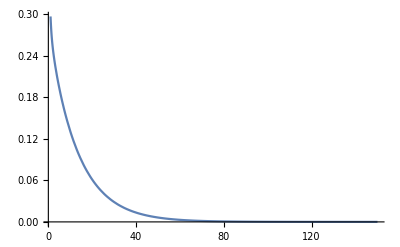

```mathematica
lp=5;
(*eb=1;*)
xx=0.1;
cc=4;
llmax=150;
sravs=0.5;
sds=-0.7;
lambdas=-3;
rr0=cc*(1-xx);
rd0=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rr0, rd0, llmax, sravs, sds, lambdas];
lambdan=Re[solv1[[1]]]
sravn=Re[solv1[[2]]]
sdn=Re[solv1[[3]]]
Plot[rl[lp, eb, rr0, rd0, sravn, sdn, lambdan, ll], {ll,1,llmax}, PlotRange->Full]
```

```mathematica
(*TODO: save interesting data to files, for a better representation*)
```

## Parameter interpolations in terms of the concentration

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.8;
sds=-0.4;
lambdas=-2.7;
xx=0.1;
lambdad={};
sravd={};
sdd={};
For[cc=1,cc<6.8,cc=cc+0.4;
rr0=cc*(1-xx);
rd0=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rr0, rd0, llmax, sravs, sds, lambdas];
lambdan=Re[solv1[[1]]];
sravn=Re[solv1[[2]]];
sdn=Re[solv1[[3]]];
AppendTo[lambdad,{cc,lambdan}];
AppendTo[sravd,{cc,sravn}];
AppendTo[sdd,{cc,sdn}];
Print[cc, " ", lambdan, " ", sravn, " ", sdn];
(*sravs=sravn;
sds=sdn;
lambdas=lambdan;*)

];
lambdaInterp=Interpolation[lambdad];
sravInterp=Interpolation[sravd];
sdInterp=Interpolation[sdd];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.4 -1.36124 2.72515×10^-9 -6.79816×10^-9

1.8 -1.31632 0.250859 -0.278426

2.2 -1.79522 0.646798 -0.419121

2.6 -2.19854 0.783479 -0.443041

3. -2.56 0.852631 -0.454498

3.4 -2.89512 0.893091 -0.461611

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {1042.16,Indeterminate,0.000366413+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-3.28616,1.,-0.469551}.

3.8 -3.03567 0.897975 -0.465935

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(149/6) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.14783,Indeterminate,0.0000104639+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-3.37539,0.891491,-0.468905}.

4.2 -3.31398 0.874643 -0.468324

General::munfl: Exp[-708.908] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.797] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.686] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {4.61553×10^11,Indeterminate,0.000114689+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-3.27707,0.84499,-0.470238}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

4.6 -3.06586 0.8 -0.4

ReplaceAll::reps: {FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of {lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

5. {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[5,4.5,0.5,srav,sd,ll] rl[5,1,4.5,0.5,srav,sd,lambda,ll])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[5,4.5,0.5,srav,sd,ll] rl[5,1,4.5,0.5,srav,sd,lambda,ll])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

5.4 {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,4.86,0.54,srav,sd,lambda,ll]==4.86,(∑_(ll=1)^150 srl[5,4.86,0.54,srav,sd,ll] rl[5,1,4.86,0.54,srav,sd,lambda,ll])/4.86==srav,sdf[4.86,0.54,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,4.86,0.54,srav,sd,lambda,ll]==4.86,(∑_(ll=1)^150 srl[5,4.86,0.54,srav,sd,ll] rl[5,1,4.86,0.54,srav,sd,lambda,ll])/4.86==srav,sdf[4.86,0.54,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

5.8 {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,5.22,0.58,srav,sd,lambda,ll]==5.22,(∑_(ll=1)^150 srl[5,5.22,0.58,srav,sd,ll] rl[5,1,5.22,0.58,srav,sd,lambda,ll])/5.22==srav,sdf[5.22,0.58,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,5.22,0.58,srav,sd,lambda,ll]==5.22,(∑_(ll=1)^150 srl[5,5.22,0.58,srav,sd,ll] rl[5,1,5.22,0.58,srav,sd,lambda,ll])/5.22==srav,sdf[5.22,0.58,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

6.2 {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,5.58,0.62,srav,sd,lambda,ll]==5.58,(∑_(ll=1)^150 srl[5,5.58,0.62,srav,sd,ll] rl[5,1,5.58,0.62,srav,sd,lambda,ll])/5.58==srav,sdf[5.58,0.62,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,5.58,0.62,srav,sd,lambda,ll]==5.58,(∑_(ll=1)^150 srl[5,5.58,0.62,srav,sd,ll] rl[5,1,5.58,0.62,srav,sd,lambda,ll])/5.58==srav,sdf[5.58,0.62,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

6.6 {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,5.94,0.66,srav,sd,lambda,ll]==5.94,(∑_(ll=1)^150 srl[5,5.94,0.66,srav,sd,ll] rl[5,1,5.94,0.66,srav,sd,lambda,ll])/5.94==srav,sdf[5.94,0.66,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,5.94,0.66,srav,sd,lambda,ll]==5.94,(∑_(ll=1)^150 srl[5,5.94,0.66,srav,sd,ll] rl[5,1,5.94,0.66,srav,sd,lambda,ll])/5.94==srav,sdf[5.94,0.66,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

7. {Re[lambda],Re[srav],Re[sd]} Re[FindRoot[{∑_(ll=1)^150 rl[5,1,6.3,0.7,srav,sd,lambda,ll]==6.3,(∑_(ll=1)^150 srl[5,6.3,0.7,srav,sd,ll] rl[5,1,6.3,0.7,srav,sd,lambda,ll])/6.3==srav,sdf[6.3,0.7,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]] Re[({lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,6.3,0.7,srav,sd,lambda,ll]==6.3,(∑_(ll=1)^150 srl[5,6.3,0.7,srav,sd,ll] rl[5,1,6.3,0.7,srav,sd,lambda,ll])/6.3==srav,sdf[6.3,0.7,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}])⟦3⟧]

General::munfl: Exp[-711.962] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.198] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-722.433] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(143/6) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. √(145/6) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.53908×10^48,Indeterminate,-0.0708106+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

FindRoot::nlnum: The function value {1.66882×10^58,Indeterminate,-0.0729728+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

FindRoot::nlnum: The function value {1.30382×10^67,Indeterminate,-0.0748367+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

$Aborted

General::munfl: Exp[-711.962] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.198] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-722.433] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(143/6) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √6 ComplexInfinity encountered.

$Aborted[]

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. √(145/6) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.53908×10^48,Indeterminate,-0.0708106+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

ReplaceAll::reps: {FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,4.5,0.5,srav,sd,lambda,ll]==4.5,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.5==srav,sdf[4.5,0.5,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}] does not exist.

FindRoot::nlnum: The function value {1.66882×10^58,Indeterminate,-0.0729728+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

ReplaceAll::reps: {FindRoot[{∑_(ll=1)^150 rl[5,1,4.86,0.54,srav,sd,lambda,ll]==4.86,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.86==srav,sdf[4.86,0.54,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,4.86,0.54,srav,sd,lambda,ll]==4.86,(∑_(ll=1)^150 srl[«6»] rl[«8»])/4.86==srav,sdf[4.86,0.54,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}] does not exist.

FindRoot::nlnum: The function value {1.30382×10^67,Indeterminate,-0.0748367+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-2.7,0.8,-0.4}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{∑_(ll=1)^150 rl[5,1,5.22,0.58,srav,sd,lambda,ll]==5.22,(∑_(ll=1)^150 srl[«6»] rl[«8»])/5.22==srav,sdf[5.22,0.58,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of {lambda,srav,sd}/.FindRoot[{∑_(ll=1)^150 rl[5,1,5.22,0.58,srav,sd,lambda,ll]==5.22,(∑_(ll=1)^150 srl[«6»] rl[«8»])/5.22==srav,sdf[5.22,0.58,srav,sd]==sd},{{lambda,-2.7},{srav,0.8,-1,1},{sd,-0.4,-1,1}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

## Isotropic-Nematic phase transition

Functions for the chemical potential and the pressure:

```mathematica
wur[lp_, rr0_, rd0_, srav_, sd_,ll_]:=-3/2*((arbar[lp, rr0, rd0, srav, sd]*ll)^2+2*arbar[lp, rr0, rd0, srav, sd]*ll)*srl[lp, rr0, rd0, srav, sd, ll];

wud[lp_, rr0_, rd0_, srav_, sd_, ll_]:=3/4*(arbar[lp, rr0, rd0, srav, sd]*ll)^2+(3/2*(arbar[lp, rr0, rd0, srav, sd]*ll)^2-3*arbar[lp, rr0, rd0, srav, sd]*ll)*srl[lp, rr0, rd0, srav, sd, ll];

sigmarod[lp_, rr0_, rd0_, srav_, sd_,ll_]:=-Log[Exp[SetPrecision[arbar[lp, rr0, rd0, srav, sd]*ll,precision]]*DawsonF[SetPrecision[√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2),precision]]/(√(3/2*arbar[lp, rr0, rd0, srav, sd]*ll))]+ arbar[lp, rr0, rd0, srav, sd]*ll*srl[lp, rr0, rd0, srav, sd, ll];

sigmadisk[lp_, rr0_, rd0_, srav_, sd_]:=-Log[Exp[SetPrecision[ad[ rr0, rd0, srav, sd],precision]]*DawsonF[SetPrecision[√((3*ad[rr0, rd0, srav, sd])/2),precision]]/(√(3/2*ad[ rr0, rd0, srav, sd]))]+ad[ rr0, rd0, srav, sd]*sd;

rli[eb_, rr0_,ll_]:=ll*Exp[eb]*(1-SetPrecision[2/(1+√(1+4*rr0*Exp[-eb])),precision])^ll;

muriso[eb_, rri_, rdi_, llmax_]:=  2*rri+2*qq*rdi+Sum[rli[eb,rri,ll]/(ll*rri)*(Log[rli[eb,rri,ll]/ll]-eb),{ll, 1,llmax}];

(*murnem [lp_, eb_, rrn_, rdn_, srav_, sd_, lambda_, llmax_]:=2*rrn*(1-5/8*srav^2)+2*qq*rdn*(1+5/4*srav*sd)+Sum[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/(ll*rrn)*(Log[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/ll]+sigmarod[lp, rrn, rdn, srav, sd,ll]-eb-2*ll/(3*lp)*Which[(rdn/(rrn+rdn))<0.5,wur[lp, rrn, rdn, srav, sd,ll],(rdn/(rrn+rdn))>=0.5,wud[lp, rrn, rdn, srav, sd, ll]]),{ll, 1,llmax}];*)
murnem [lp_, eb_, rr0_, rd0_, srav_, sd_, lambda_, llmax_]:=2*rr0*(1-5/8*srav^2)+2*qq*rd0*(1+5/4*srav*sd)+Sum[rl[lp, eb, rr0, rd0, srav, sd, lambda, ll]/(ll*rr0)*(Log[rl[lp, eb, rr0, rd0, srav, sd, lambda, ll]/ll]+sigmarod[lp, rr0, rd0, srav, sd,ll]-eb-2*ll/(3*lp)*wur[lp, rr0, rd0, srav, sd, ll]),{ll, 1,llmax}];

mudiso[rri_, rdi_]:=Log[rdi]+2*zz*rdi+2*qq*rri;

mudnem[lp_, rrn_, rdn_, srav_, sd_]:=Log[rdn]+sigmadisk[lp, rrn, rdn, srav, sd]+2*zz*rdn*(1-5/8*sd^2)+2*qq*rrn*(1+5/4*srav*sd);

pressureiso[eb_, rri_,rdi_, llmax_]:=Sum[rli[eb,rri,ll]/ll,{ll,1,llmax}]+rdi+rri^2+2*qq*rri*rdi+zz*rdi^2;

pressurenem[lp_, eb_, rrn_, rdn_, srav_, sd_, lambda_, llmax_]:=Sum[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/ll,{ll,1,llmax}]+rdn+rrn^2*(1-5/8 srav^2)+2*qq*rrn*rdn*(1+5/4*srav*sd)+zz*rdn^2*(1-5/8*sd^2);
```

Equation system to obtain OverBar[S_r], S_d, λ, c_i, c_n, x_n:

```mathematica
solveConditions2[lp_, eb_,llmax_, sravs_, sds_, lambdas_, rri_, rrns_, rdis_, rdns_]:=(n=0;
FindRoot[{
Sum[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll],{ll,1,llmax}]-rrn,
rrn^-1*Sum[srl[lp,rrn, rdn, srav, sd, ll]*rl[lp, eb, rrn, rdn, srav, sd, lambda, ll],{ll,1,llmax}]-srav,
sdf[rrn,rdn,srav,sd]-sd,

muriso[eb, rri, rdi, llmax]-murnem[lp, eb, rrn, rdn, srav, sd, lambda, llmax],
mudiso[rri,rdi]-mudnem[lp,rrn, rdn, srav, sd],
pressureiso[eb, rri,rdi, llmax]-pressurenem[lp, eb, rrn, rdn, srav, sd, lambda, llmax]

},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}, {rrn, rrns,10^-5,10}, {rdi,rdis,10^-5,10}, {rdn,rdns,10^-5,10}},EvaluationMonitor:>(n++;Print[{n}])]);
pressure [lp_, eb_,llmax_, sravs_, sds_, lambdas_, xxns_, ccis_, ccns_, xxi_]:= (
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
solv2 = {lambda,srav, sd, rrn,rdi,rdn}/.solveConditions2[lp, eb, llmax, sravs, sds, lambdas, rri, rrns, rdis, rdns];
lambdan=Re[solv2[[1]]];
sravn=Re[solv2[[2]]];
sdn=Re[solv2[[3]]];
rrnn=Re[solv2[[4]]];
rdin=Re[solv2[[5]]];
rdnn=Re[solv2[[6]]];
xxnn=rdnn/(rrnn+rdnn);
ccin=rri+rdin;
ccnn=rrnn+rdnn;
{xxi, pressureiso[eb, rri,rdin, llmax],xxnn,pressurenem[lp, eb, rrnn, rdnn, sravn, sdn, lambdan, llmax],lambdan, sravn,sdn,ccin,ccnn}
)
```

### Plot

```mathematica
lp=5;
(*eb=1;*)
llmax=150;
sravs=0.9284;
sds=-0.46857;
lambdas=-3.368;
xxi=0.1;
xxns=0.11;
ccis=3.6;
ccns=4.4;
(*Plot[pressure [lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi][[2]], {xxi,0.01,0.99},PlotPoints->4, PlotRange->Full]*)
pressure[lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi]
```

General::munfl: Exp[-713.613] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.978] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.344] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(139/6) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(35/6) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. √(47/2) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {4.52167×10^12,Indeterminate,-0.00269566+0. ⅈ,Indeterminate,3.3884+0. ⅈ,-3.38654×10^10} is not a list of numbers with dimensions {6} at {lambda,srav,sd,rrn,rdi,rdn} = {-3.368,0.9284,-0.46857,3.916,0.36,0.484}.

$Aborted

## Draft/Tests

With the While-Loop:

```mathematica
solveConditions3[lp_, eb_,llmax_, srav_, sd_, lambda_, rri_, rrns_, rdis_, rdns_]:=FindRoot[{

muriso[eb, rri, rdi, llmax]==murnem[lp, eb, rrn, rdn, srav, sd, lambda, llmax],
mudiso[rri,rdi]==mudnem[lp,rrn, rdn, srav, sd],
pressureiso[eb, rri,rdi, llmax]==pressurenem[lp, eb, rrn, rdn, srav, sd, lambda, llmax]

},{{rrn, rrns,10^-5,10}, {rdi,rdis,10^-5,10}, {rdn,rdns,10^-5,10}}];
```

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.8624569216635748;
sds=-0.40577124411248866;
lambdas=-2.9689877260665503;
xxi=0.1;
xxns=0.01;
ccis=3.6029484239166867;
ccns=3.9801539278678573;
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
df=100;

While[df>1,
solv2 = {lambda,srav, sd}/.solveConditions[lp, eb,rrns,rdns,llmax, sravs, sds, lambdas];
lambdan=Re[solv2[[1]]];
sravn=Re[solv2[[2]]];
sdn=Re[solv2[[3]]];
Print[lambdan, sravn, sdn];

solv3 = {rrn,rdi,rdn}/.solveConditions3[lp, eb,llmax, sravn, sdn, lambdan, rri, rrns, rdis, rdns];
rrnn=Re[solv3[[1]]];
rdin=Re[solv3[[2]]];
rdnn=Re[solv3[[3]]];
df=10^5*Max[{Abs[sravs-sravn],Abs[sds-sdn],Abs[lambdas-lambdan],Abs[rdis-rdin],Abs[rrns-rrnn],Abs[rdns-rdnn]}];
sravs=sravn;
sds=sdn;
lambdas=lambdan;
rdis=rdin;
rrns=rrnn;
rdns=rdnn;
Print[df]
];
xxnn=rdnn/(rrnn+rdnn);
ccin=rri+rdin;
ccnn=rrnn+rdnn;
{xxi, pressureiso[eb, rri,rdin, llmax],xxnn,pressurenem[lp, eb, rrnn, rdnn, sravn, sdn, lambdan, llmax]}
{lambdan, sravn, sdn, xxnn, ccin, ccnn}
```

-3.124310.922809-0.445131

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

359907.

-2.288834.1716×10^-8-2.29122×10^-8

FindRoot::reged: The point {0.931136+0. ⅈ,7.71567+0. ⅈ,10.+0. ⅈ} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

748833.

-1.549023.04969×10^-9-8.57716×10^-10

FindRoot::reged: The point {0.931136,7.71567,10.} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

73981.1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-1.549023.04968×10^-9-8.57716×10^-10

FindRoot::reged: The point {0.931136,7.71567,10.} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

3.18084×10^-10

{0.1,129.707,0.914818,130.223}

{-1.54902,3.04968×10^-9,-8.57716×10^-10,0.914818,10.9583,10.9311}

```mathematica
Integrate[Exp[a*x^2]*Sin[x], {x, 0, Pi}]
```

(ⅇ^(1/4/a) √π (-2 Erf[1/(2 √a)]+Erf[(1-2 ⅈ a π)/(2 √a)]+Erf[(1+2 ⅈ a π)/(2 √a)]))/(4 √a)

```mathematica
DawsonF[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2)]
```

General::munfl: Exp[-730.897] is too small to represent as a normalized machine number; precision may be lost.

0.0185071

```mathematica
DawsonF[SetPrecision[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2),20]]
```

0.01850715269772228

```mathematica
(1.000000082740371*^-10)^-1*Sum[srl[5,1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, ll]*rl[5, 1, 1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, -4.765905785346516, ll],{ll,1,150}]
```

7.23822×10^8

```mathematica
s=Exp[x]*DawsonF[√((3*x)/2)]/√((3*x)/2);
Plot[x,s]
```

Plot::pllim: Range specification s is not of the form {x, xmin, xmax}.

Plot[x,s]

```mathematica
Plot[s,{x,0,50}]
```

-Graphics-

```mathematica
(2/(1+√(1+4*4*Exp[-1])))^-1
```

1/2 (1+√(1+16/ⅇ))

```mathematica
N[1/2 (1+√(1+16/ⅇ))]
```

1.81207